## Simplified FK of SRSPM

```mathematica
SetDirectory[NotebookDirectory[]]
(*<<ed5314utils_en.m*)
```

/home/nightmareforev/git/root_tracking/Mathematica/SRSPM

```mathematica
rotZ[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
(*fixed platform*)
b1 = {1, 0, 0};
b2 = rotZ[2*0.2985].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
tempa = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[rotZ[(2π/3-2*0.2985)/2].tempa[[i]],{i, Length[tempa]}];
ashift=b-{b[[1]],b[[1]],b[[1]],b[[1]],b[[1]],b[[1]]}
```

{{0.,0.,0.},{-0.509373,0.294087,0.},{-1.68835,-0.386598,0.},{-1.68835,-0.974772,0.},{-0.509373,-1.65546,0.},{-2.22045×10^-16,-1.36137,0.}}

```mathematica
(*moving platform*)
a1 = {0.5803, 0, 0};
a2 = rotZ[2*0.6573].a1;
a3 = rotZ[2π/3].a1;
a4 = rotZ[2π/3].a2;
a5 = rotZ[4π/3].a1;
a6 = rotZ[4π/3].a2;
tempa = Table[Symbol["a"<>ToString[i]],{i, 6}];
a = Table[rotZ[(2π/3-2*0.6573)/2].tempa[[i]],{i, Length[tempa]}];
ashift=a-{a[[1]],a[[1]],a[[1]],a[[1]],a[[1]],a[[1]]}
```

{{0.,0.,0.},{-0.614103,0.354553,0.},{-0.996139,0.133984,0.},{-0.996139,-0.575121,0.},{-0.614103,-0.795689,0.},{-1.11022×10^-16,-0.441137,0.}}

```mathematica
(*lvals for circle tracking example*)
```

```mathematica
(*lvals = {1.4458208723874426,1.568679047566447,1.57865471573012,1.3393859531342835,1.152479064455009,1.286875291086054}*)
```

```mathematica
(*lvals for singularity example*)
```

```mathematica
lvals = {1.5606305002994023,1.5251471621309471,1.3150462596882393,1.1300948138280011,1.1268160733797703,1.5034746579174754}
```

{1.56063,1.52515,1.31505,1.13009,1.12682,1.50347}

```mathematica
l = {l1, l2, l3, l4, l5, l6}
```

{l1,l2,l3,l4,l5,l6}

```mathematica
sub={b2x->-0.5093734006873172,b2y->0.2940868700048578,b2z->0,b3x->-1.6883547421176872,b3y->-0.3865983248395124,b3z->0,b4x->-1.6883547421176874,b4y->-0.9747720648492277,b4z->0,b5x->-0.5093734006873175,b5y->-1.6554572596935981,b5z->0,b6x->-2.220446049250313*10^-16,b6y->-1.3613703896887406,b6z->0,t2x->-0.6141031970306339,t2y->0.35455264611584647,t2z->0,t3x->-0.9961387846155708,t3y->0.13398429678366627,t3z->0,t4x->-0.996138784615571,t4y->-0.5751209954480264,t4z->0,t5x->-0.6141031970306341,t5y->-0.7956893447802065,t5z->0,t6x->-1.1102230246251565*10^-16,t6y->-0.44113669866436034,t6z->0}
len=Inner[Rule, l, lvals, List]
```

{b2x→-0.509373,b2y→0.294087,b2z→0,b3x→-1.68835,b3y→-0.386598,b3z→0,b4x→-1.68835,b4y→-0.974772,b4z→0,b5x→-0.509373,b5y→-1.65546,b5z→0,b6x→-2.22045×10^-16,b6y→-1.36137,b6z→0,t2x→-0.614103,t2y→0.354553,t2z→0,t3x→-0.996139,t3y→0.133984,t3z→0,t4x→-0.996139,t4y→-0.575121,t4z→0,t5x→-0.614103,t5y→-0.795689,t5z→0,t6x→-1.11022×10^-16,t6y→-0.441137,t6z→0}

{l1→1.56063,l2→1.52515,l3→1.31505,l4→1.13009,l5→1.12682,l6→1.50347}

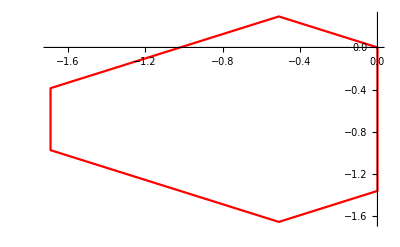

```mathematica
(*Fixed Platform*)
o1={0,0,0};
o2={b2x,b2y,b2z};
o3={b3x,b3y,b3z};
o4={b4x,b4y,b4z};
o5={b5x,b5y,b5z};
o6={b6x,b6y,b6z};
o={o1,o2,o3,o4,o5,o6,o1};
ListLinePlot[(o/.sub)[[;;, 1;;2]],PlotStyle->Red]
(*oj={bjx,bjy,bjz};*)
```

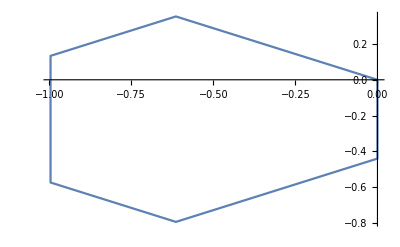

```mathematica
(*Moving platform*)
p1={0,0,0};
p2={t2x,t2y,t2z};
p3={t3x,t3y,t3z};
p4={t4x,t4y,t4z};
p5={t5x,t5y,t5z};
p6={t6x,t6y,t6z};
p={p1,p2,p3,p4,p5,p6,p1};
ListLinePlot[(p/.sub)[[;;, 1;;2]]]
(*pj={tjx,tjy,tjz};*)
```

```mathematica
Cmat={{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}
```

{{0,-c3,c2},{c3,0,-c1},{-c2,c1,0}}

```mathematica
Rmat=Simplify[(IdentityMatrix[3]+Cmat).Inverse[(IdentityMatrix[3]-Cmat)]];
```

```mathematica
xvec={x,y,z};
```

```mathematica
p1o=xvec+Rmat.p1;
p2o=xvec+Rmat.p2;
p3o=xvec+Rmat.p3;
p4o=xvec+Rmat.p4;
p5o=xvec+Rmat.p5;
p6o=xvec+Rmat.p6;
(*pjo=xvec+Rmat.pj;*)
```

```mathematica
eq1=(p1o-o1).(p1o-o1)-l1^2
```

-l1^2+x^2+y^2+z^2

```mathematica
(*monoprod[{a_,b_}]:=a.b;
eqj=FullSimplify[monoprod[FullSimplify[monopoly[Factor[(pjo-oj).(pjo-oj)-lj^2][[3]],{bjx,bjy,bjz,tjx,tjy,tjz,lj}]]/.{ (x^2+y^2+z^2)-> w,1+c1^2+c2^2+c3^2-> c0,-1-c1^2-c2^2-c3^2-> -c0}]];*)
```

```mathematica
eq2=FullSimplify[Factor[(p2o-o2).(p2o-o2)-l2^2][[3]]];
eq3=FullSimplify[Factor[(p3o-o3).(p3o-o3)-l3^2][[3]]];
eq4=FullSimplify[Factor[(p4o-o4).(p4o-o4)-l4^2][[3]]];
eq5=FullSimplify[Factor[(p5o-o5).(p5o-o5)-l5^2][[3]]];
eq6=FullSimplify[Factor[(p6o-o6).(p6o-o6)-l6^2][[3]]];
```

```mathematica
nsol=Timing[NSolve[N[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len),50]=={0,0,0,0,0,0},{x,y,z,c1,c2,c3},Method-> "HomotopyContinuation"]];
```

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

```mathematica
len
```

{l1→1.56063,l2→1.52515,l3→1.31505,l4→1.13009,l5→1.12682,l6→1.50347}

```mathematica
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@nsol[[2]](*Residue check*)
```

{1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.14181×10^20,1.14181×10^20,7.40635×10^19,7.40635×10^19,3.60977×10^20,3.60977×10^20,1.08295×10^20,1.08295×10^20,1.47038×10^18,1.47038×10^18,2.70781×10^17,2.70781×10^17,1.19152×10^18,1.19152×10^18,2.26779×10^18,2.26779×10^18,9.04762×10^17,9.04762×10^17,4.42185×10^19,4.42185×10^19,3.58212×10^19,3.58212×10^19,4.54954×10^17,4.54954×10^17,1.09397×10^18,1.09397×10^18,1.02686×10^18,1.02686×10^18,9.51353×10^17,9.51353×10^17,6.76953×10^17,6.76953×10^17,9.04762×10^17,9.04762×10^17,4.42185×10^19,4.42185×10^19,3.58212×10^19,3.58212×10^19,4.54954×10^17,4.54954×10^17,3.35898×10^17,3.35898×10^17,2.98317×10^16,2.98317×10^16,2.33467×10^16,2.33467×10^16,1.27573×10^17,1.27573×10^17,5.72344×10^16,5.72344×10^16,6.39344×10^16,6.39344×10^16,3.92524×10^16,3.92524×10^16,5.80955×10^16,5.80955×10^16,3.60647×10^16,3.60647×10^16,2.46661×10^16,2.46661×10^16,3.21932×10^16,3.21932×10^16,2.77114×10^16,2.77114×10^16,2.46661×10^16,2.46661×10^16,2.77114×10^16,2.77114×10^16,3.60647×10^16,3.60647×10^16,3.21932×10^16,3.21932×10^16,3.92524×10^16,3.92524×10^16,5.72344×10^16,5.72344×10^16,5.80955×10^16,5.80955×10^16,6.39344×10^16,6.39344×10^16,2.94489×10^18,2.94489×10^18,6.02576×10^14,6.02576×10^14,1.72538×10^15,1.72538×10^15,2.15383×10^18,2.15383×10^18,7.83816×10^17,7.83816×10^17,5.8×10^17,5.8×10^17,5.8×10^17,5.8×10^17,4.4398×10^16,4.4398×10^16,4.4398×10^16,4.4398×10^16,6.44302×10^15,6.44302×10^15,8.5817×10^15,8.5817×10^15,8.5817×10^15,8.5817×10^15,1.55838×10^16,1.55838×10^16,947672.,947672.,1.98458×10^6,1.98458×10^6,1.98458×10^6,1.98458×10^6,287989.,287989.,182313.,182313.,182313.,182313.,84960.5,84960.5,99993.3,99993.3,99993.3,99993.3,3.11344×10^-13,3.11344×10^-13,9.48195×10^-13,9.48195×10^-13,9.54123×10^-14,9.54123×10^-14,4.88463×10^-14,4.88463×10^-14,9.54123×10^-14,9.54123×10^-14,1.38898×10^-14,1.38898×10^-14,1.33227×10^-14,1.33227×10^-14,3.11061×10^-15,3.11061×10^-15,1.42178×10^-15,1.42178×10^-15,8.14105×10^-15,1.88738×10^-15,1.69104×10^-15,1.88738×10^-15,1.69104×10^-15,2.29953×10^-15,2.29953×10^-15,6.88696×10^-15,8.14105×10^-15,6.88696×10^-15}

```mathematica
nsol[[2]][[3]]
```

{x→-2.28056×10^17-7.28995×10^17 ⅈ,y→7.26736×10^17-2.2371×10^17 ⅈ,z→-6.62991×10^16+5.54034×10^16 ⅈ,c1→0.772379-0.517395 ⅈ,c2→0.554854+0.875733 ⅈ,c3→-0.0920629+0.937177 ⅈ}

```mathematica
Select[c3/.nsol[[2]],Abs[Im[#]]≤ 10^-6&](*Reals filter*)
```

{-1.21096+2.63769×10^-45 ⅈ,-1.21096-2.63769×10^-45 ⅈ,0.825788-6.49487×10^-46 ⅈ,0.825788+6.49487×10^-46 ⅈ,0.825788-6.49487×10^-46 ⅈ,0.825788+6.49487×10^-46 ⅈ,-1.21096+2.63769×10^-45 ⅈ,-1.21096-2.63769×10^-45 ⅈ,1.67247-2.15139×10^-44 ⅈ,1.67247+2.15139×10^-44 ⅈ,-0.597917+1.15504×10^-45 ⅈ,-0.597917-1.15504×10^-45 ⅈ,-0.597917+1.15504×10^-45 ⅈ,-0.597917-1.15504×10^-45 ⅈ,1.67247-2.15139×10^-44 ⅈ,1.67247+2.15139×10^-44 ⅈ,-3.22454+7.07945×10^-43 ⅈ,-3.22454-7.07945×10^-43 ⅈ,0.310122-7.69602×10^-47 ⅈ,0.310122+7.69602×10^-47 ⅈ,0.310122-7.69601×10^-47 ⅈ,0.310122+7.69601×10^-47 ⅈ,-3.22454+7.07945×10^-43 ⅈ,-3.22454-7.07945×10^-43 ⅈ,48.9051+2.62491×10^-40 ⅈ,48.9051-2.62491×10^-40 ⅈ,-0.0204478,-0.0204478,-0.0204478,-0.0204478,48.9051+2.62492×10^-40 ⅈ,48.9051-2.62492×10^-40 ⅈ,286092.+7.58109×10^-29 ⅈ,286092.-7.58109×10^-29 ⅈ,-221217.+4.19601×10^-29 ⅈ,-221217.-4.19601×10^-29 ⅈ,194308.+7.77316×10^-29 ⅈ,194308.-7.77316×10^-29 ⅈ,-1.35802×10^-6+4.22179×10^-49 ⅈ,-1.35802×10^-6-4.22179×10^-49 ⅈ,1.7563×10^-6-1.13015×10^-47 ⅈ,1.7563×10^-6+1.13015×10^-47 ⅈ,-1.99952×10^-6+1.16461×10^-47 ⅈ,-1.99952×10^-6-1.16461×10^-47 ⅈ,14.3569-3.27294×10^-31 ⅈ,14.3569+3.27294×10^-31 ⅈ,16.2963-5.44969×10^-31 ⅈ,16.2963+5.44969×10^-31 ⅈ,-1.31505-8.22257×10^-31 ⅈ,-1.31505+8.22257×10^-31 ⅈ,-0.879938-7.22416×10^-32 ⅈ,-0.879938+7.22416×10^-32 ⅈ,-0.292305+2.29537×10^-32 ⅈ,-0.292305-2.29537×10^-32 ⅈ,0.0428234+7.58731×10^-35 ⅈ,0.0428234-7.58731×10^-35 ⅈ,0.039926+6.11308×10^-34 ⅈ,0.039926-6.11308×10^-34 ⅈ,0.173679,0.1,0.104256,0.1,0.104256,0.0370171+5.47065×10^-33 ⅈ,0.0370171-5.47065×10^-33 ⅈ,0.219325,0.173679,0.219325}

```mathematica
(*Coefficient[Times@@(α{2,4,4,4,4,4}),α^6]
Coefficient[Times@@(α{2,3,3,3,3,3}),α^6]
Coefficient[Times@@(α{2,2,2,2,2,2}+β{0,2,2,2,2,2}),α^3 β^3]
Coefficient[Times@@(α{2,1,1,1,1,1}+β{0,2,2,2,2,2}),α^3 β^3]*)(*multi-homogenoeus Bezout number calculation for different grouping and formulation*)
```

## Use these solutions till I figure out how to get the others

```mathematica
reqsol=nsol[[2,-14;;]];
```

```mathematica
(* Residue check *)
Norm[Flatten[({eq1,eq2,eq3,eq4,eq5,eq6}/.sub/.len/.#)] ]&/@reqsol
```

{3.11061×10^-15,3.11061×10^-15,1.42178×10^-15,1.42178×10^-15,8.14105×10^-15,1.88738×10^-15,1.69104×10^-15,1.88738×10^-15,1.69104×10^-15,2.29953×10^-15,2.29953×10^-15,6.88696×10^-15,8.14105×10^-15,6.88696×10^-15}

### These are solutions for the center of the moving platform

```mathematica
transformedsol=Table[Inner[Rule,{x,y,z,c1,c2,c3},(Join[(rotZ[(2π/3-2*0.2985)/2].{1,0,0}+{x,y,z}-Rmat.rotZ[(2π/3-2*0.6573)/2].{0.5803,0,0}),{c1,c2,c3}]/.reqsol[[ii]]),List],{ii,1,14}];
```

```mathematica
(* x y z c1 c2 c3 *)
```

```mathematica
transformedsol//MatrixForm
```

(x→1.66906+2.14238×10^-30 ⅈ | y→-0.542491+7.56363×10^-31 ⅈ | z→1.35872×10^-30-0.558445 ⅈ | c1→-2.55977×10^-32-0.118959 ⅈ | c2→3.8601×10^-31+0.70675 ⅈ | c3→0.0428234+7.58731×10^-35 ⅈ
x→1.66906-2.14238×10^-30 ⅈ | y→-0.542491-7.56363×10^-31 ⅈ | z→1.35872×10^-30+0.558445 ⅈ | c1→-2.55977×10^-32+0.118959 ⅈ | c2→3.8601×10^-31-0.70675 ⅈ | c3→0.0428234-7.58731×10^-35 ⅈ
x→-1.27828-1.58591×10^-31 ⅈ | y→1.51748+7.60883×10^-32 ⅈ | z→5.86656×10^-31-1.00336 ⅈ | c1→2.21046×10^-31-0.673211 ⅈ | c2→9.43976×10^-32-0.305329 ⅈ | c3→0.039926+6.11308×10^-34 ⅈ
x→-1.27828+1.58591×10^-31 ⅈ | y→1.51748-7.60883×10^-32 ⅈ | z→5.86656×10^-31+1.00336 ⅈ | c1→2.21046×10^-31+0.673211 ⅈ | c2→9.43976×10^-32+0.305329 ⅈ | c3→0.039926-6.11308×10^-34 ⅈ
x→-0.726545 | y→-0.215867 | z→-0.710016 | c1→-0.150743 | c2→-0.962838 | c3→0.173679
x→0.1 | y→0.2 | z→1.2 | c1→0.3 | c2→-0.2 | c3→0.1
x→0.134547 | y→0.248613 | z→1.1708 | c1→0.356827 | c2→-0.224341 | c3→0.104256
x→0.1 | y→0.2 | z→-1.2 | c1→-0.3 | c2→0.2 | c3→0.1
x→0.134547 | y→0.248613 | z→-1.1708 | c1→-0.356827 | c2→0.224341 | c3→0.104256
x→-1.46731+6.18604×10^-31 ⅈ | y→-1.67788+1.45435×10^-30 ⅈ | z→-1.54019×10^-30-1.36029 ⅈ | c1→1.60324×10^-31+0.693344 ⅈ | c2→-1.26728×10^-31-0.314086 ⅈ | c3→0.0370171+5.47065×10^-33 ⅈ
x→-1.46731-6.18604×10^-31 ⅈ | y→-1.67788-1.45435×10^-30 ⅈ | z→-1.54019×10^-30+1.36029 ⅈ | c1→1.60324×10^-31-0.693344 ⅈ | c2→-1.26728×10^-31+0.314086 ⅈ | c3→0.0370171-5.47065×10^-33 ⅈ
x→-0.463395 | y→-0.797546 | z→-0.330448 | c1→0.595271 | c2→1.04779 | c3→0.219325
x→-0.726545 | y→-0.215867 | z→0.710016 | c1→0.150743 | c2→0.962838 | c3→0.173679
x→-0.463395 | y→-0.797546 | z→0.330448 | c1→-0.595271 | c2→-1.04779 | c3→0.219325)

```mathematica
Chop[transformedsol]//MatrixForm
```

(x→1.66906 | y→-0.542491 | z→0.-0.558445 ⅈ | c1→0.-0.118959 ⅈ | c2→0.+0.70675 ⅈ | c3→0.0428234
x→1.66906 | y→-0.542491 | z→0.+0.558445 ⅈ | c1→0.+0.118959 ⅈ | c2→0.-0.70675 ⅈ | c3→0.0428234
x→-1.27828 | y→1.51748 | z→0.-1.00336 ⅈ | c1→0.-0.673211 ⅈ | c2→0.-0.305329 ⅈ | c3→0.039926
x→-1.27828 | y→1.51748 | z→0.+1.00336 ⅈ | c1→0.+0.673211 ⅈ | c2→0.+0.305329 ⅈ | c3→0.039926
x→-0.726545 | y→-0.215867 | z→-0.710016 | c1→-0.150743 | c2→-0.962838 | c3→0.173679
x→0.1 | y→0.2 | z→1.2 | c1→0.3 | c2→-0.2 | c3→0.1
x→0.134547 | y→0.248613 | z→1.1708 | c1→0.356827 | c2→-0.224341 | c3→0.104256
x→0.1 | y→0.2 | z→-1.2 | c1→-0.3 | c2→0.2 | c3→0.1
x→0.134547 | y→0.248613 | z→-1.1708 | c1→-0.356827 | c2→0.224341 | c3→0.104256
x→-1.46731 | y→-1.67788 | z→0.-1.36029 ⅈ | c1→0.+0.693344 ⅈ | c2→0.-0.314086 ⅈ | c3→0.0370171
x→-1.46731 | y→-1.67788 | z→0.+1.36029 ⅈ | c1→0.-0.693344 ⅈ | c2→0.+0.314086 ⅈ | c3→0.0370171
x→-0.463395 | y→-0.797546 | z→-0.330448 | c1→0.595271 | c2→1.04779 | c3→0.219325
x→-0.726545 | y→-0.215867 | z→0.710016 | c1→0.150743 | c2→0.962838 | c3→0.173679
x→-0.463395 | y→-0.797546 | z→0.330448 | c1→-0.595271 | c2→-1.04779 | c3→0.219325)

```mathematica
roots = transformedsol
```

{{x→1.66906+2.14238×10^-30 ⅈ,y→-0.542491+7.56363×10^-31 ⅈ,z→1.35872×10^-30-0.558445 ⅈ,c1→-2.55977×10^-32-0.118959 ⅈ,c2→3.8601×10^-31+0.70675 ⅈ,c3→0.0428234+7.58731×10^-35 ⅈ},{x→1.66906-2.14238×10^-30 ⅈ,y→-0.542491-7.56363×10^-31 ⅈ,z→1.35872×10^-30+0.558445 ⅈ,c1→-2.55977×10^-32+0.118959 ⅈ,c2→3.8601×10^-31-0.70675 ⅈ,c3→0.0428234-7.58731×10^-35 ⅈ},{x→-1.27828-1.58591×10^-31 ⅈ,y→1.51748+7.60883×10^-32 ⅈ,z→5.86656×10^-31-1.00336 ⅈ,c1→2.21046×10^-31-0.673211 ⅈ,c2→9.43976×10^-32-0.305329 ⅈ,c3→0.039926+6.11308×10^-34 ⅈ},{x→-1.27828+1.58591×10^-31 ⅈ,y→1.51748-7.60883×10^-32 ⅈ,z→5.86656×10^-31+1.00336 ⅈ,c1→2.21046×10^-31+0.673211 ⅈ,c2→9.43976×10^-32+0.305329 ⅈ,c3→0.039926-6.11308×10^-34 ⅈ},{x→-0.726545,y→-0.215867,z→-0.710016,c1→-0.150743,c2→-0.962838,c3→0.173679},{x→0.1,y→0.2,z→1.2,c1→0.3,c2→-0.2,c3→0.1},{x→0.134547,y→0.248613,z→1.1708,c1→0.356827,c2→-0.224341,c3→0.104256},{x→0.1,y→0.2,z→-1.2,c1→-0.3,c2→0.2,c3→0.1},{x→0.134547,y→0.248613,z→-1.1708,c1→-0.356827,c2→0.224341,c3→0.104256},{x→-1.46731+6.18604×10^-31 ⅈ,y→-1.67788+1.45435×10^-30 ⅈ,z→-1.54019×10^-30-1.36029 ⅈ,c1→1.60324×10^-31+0.693344 ⅈ,c2→-1.26728×10^-31-0.314086 ⅈ,c3→0.0370171+5.47065×10^-33 ⅈ},{x→-1.46731-6.18604×10^-31 ⅈ,y→-1.67788-1.45435×10^-30 ⅈ,z→-1.54019×10^-30+1.36029 ⅈ,c1→1.60324×10^-31-0.693344 ⅈ,c2→-1.26728×10^-31+0.314086 ⅈ,c3→0.0370171-5.47065×10^-33 ⅈ},{x→-0.463395,y→-0.797546,z→-0.330448,c1→0.595271,c2→1.04779,c3→0.219325},{x→-0.726545,y→-0.215867,z→0.710016,c1→0.150743,c2→0.962838,c3→0.173679},{x→-0.463395,y→-0.797546,z→0.330448,c1→-0.595271,c2→-1.04779,c3→0.219325}}

```mathematica
Join[roots[[5;; 8]], roots[[11;;]]]//Chop//MatrixForm
```

(x→-0.726545 | y→-0.215867 | z→-0.710016 | c1→-0.150743 | c2→-0.962838 | c3→0.173679
x→0.1 | y→0.2 | z→1.2 | c1→0.3 | c2→-0.2 | c3→0.1
x→0.134547 | y→0.248613 | z→1.1708 | c1→0.356827 | c2→-0.224341 | c3→0.104256
x→0.1 | y→0.2 | z→-1.2 | c1→-0.3 | c2→0.2 | c3→0.1
x→-1.46731 | y→-1.67788 | z→0.+1.36029 ⅈ | c1→0.-0.693344 ⅈ | c2→0.+0.314086 ⅈ | c3→0.0370171
x→-0.463395 | y→-0.797546 | z→-0.330448 | c1→0.595271 | c2→1.04779 | c3→0.219325
x→-0.726545 | y→-0.215867 | z→0.710016 | c1→0.150743 | c2→0.962838 | c3→0.173679
x→-0.463395 | y→-0.797546 | z→0.330448 | c1→-0.595271 | c2→-1.04779 | c3→0.219325)